## Numerical Example Ambartsumyan et al. CMAME (2020) :

### Displacement :

```mathematica
u[x_,y_]:={x,y}
```

Dirichlet boundary conditions : (they are not homogeneous)

```mathematica
u[0,y]
```

{0,y}

```mathematica
u[1,y]
```

{1,y}

```mathematica
u[x,0]
```

{x,0}

```mathematica
u[x,1]
```

{x,1}

ContourPlot of the Magnitude of the displacement (Euclidean norm) :

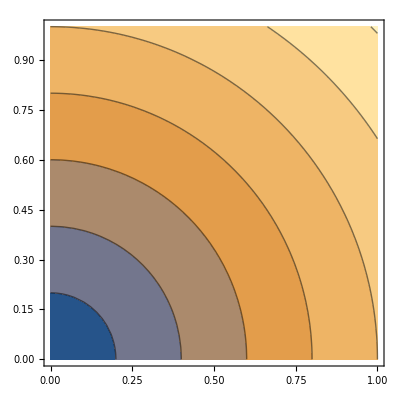

```mathematica
ContourPlot[Sqrt[(x)^2+(y)^2],{x,0,1},{y,0,1}]
```

### Pressure:

```mathematica
p[x_,y_]:= x(1-x)y(1-y)
```

```mathematica
p[0,y]
```

0

```mathematica
p[1,y]
```

0

```mathematica
p[x,0]
```

0

```mathematica
p[x,1]
```

0

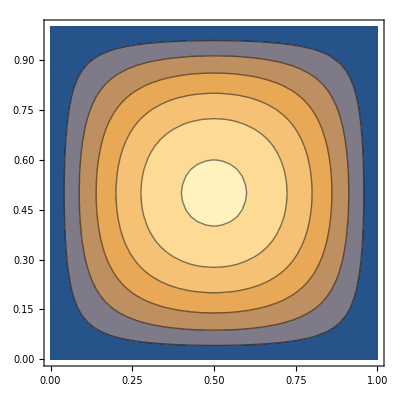

```mathematica
ContourPlot[p[x,y],{x,0,1},{y,0,1}]
```

### Elastic Stress:

```mathematica
{D[(x), x],D[(x), y]}//Simplify
```

{1,0}

```mathematica
{D[(y), x],D[(y), y]}//Simplify
```

{0,1}

```mathematica
Gradu:={{1,0},{0,1}}
```

Let us define ϵ (u) :

```mathematica
1/2*(Gradu+Transpose[Gradu])//Simplify
```

{{1,0},{0,1}}

```mathematica
mu=μ
lambda=λ
```

μ

λ

Let us compute the stress σ= A^-1 ϵ(u): (Using the expression for A^-1 given in equation (3 . 2 . 9) of Ambartsumyan PhD. Thesis)

```mathematica
2 mu {{1,0},{0,1}}+lambda {{2,0},{0,2}}//Simplify
```

{{2 (λ+μ),0},{0,2 (λ+μ)}}

Let us define the stress function as the previous expression :

```mathematica
Sigmae:={{2 (λ+μ),0},{0,2 (λ+μ)}}
```

### Stress:

```mathematica
Sigmae-alpha {{p[x,y],0},{0,p[x,y]}}//Simplify
```

{{alpha x y (-1+x+y-x y)+2 (λ+μ),0},{0,alpha x y (-1+x+y-x y)+2 (λ+μ)}}

```mathematica
Sigma[x_,y_]:={{alpha x y (-1+x+y-x y)+2 (λ+μ),0},{0,alpha x y (-1+x+y-x y)+2 (λ+μ)}}
```

ContourPlot of the Magnitude of the first row of σ :

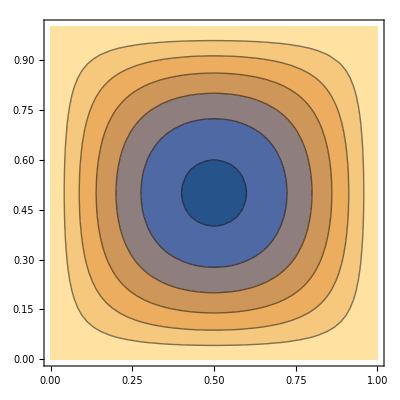

```mathematica
ContourPlot[Sqrt[(alpha x y (-1+x+y-x y)+2 (λ+μ))^2+(0)^2]/.{λ ->0,μ->1,alpha->1},{x,0,1},{y,0,1}]
```

ContourPlot of the Magnitude of the second row of σ :

```mathematica
ContourPlot[Sqrt[(0)^2+(alpha x y (-1+x+y-x y)+2 (λ+μ))^2]/.{λ ->0,μ->1,alpha->1},{x,0,1},{y,0,1}]
```

-Graphics-

### Rotation :

```mathematica
1/2*(Gradu-Transpose[Gradu])//Simplify
```

{{0,0},{0,0}}

ContourPlot of the element in the first row and second column of the rotation:

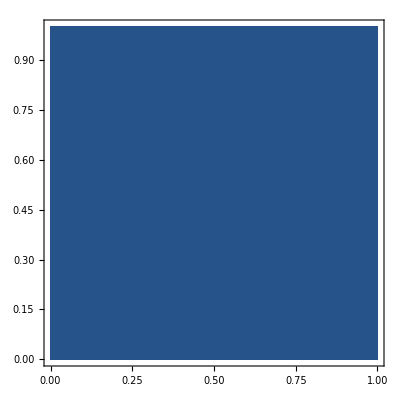

```mathematica
ContourPlot[0,{x,0,1},{y,0,1}]
```

### Darcy velocity :

```mathematica
KK:=perm*{{1, 0},{0, 1}}
```

```mathematica
-KK.{D[p[x,y],x],D[p[x,y],y]}//Simplify
```

{-perm (-1+2 x) (-1+y) y,-perm (-1+x) x (-1+2 y)}

```mathematica
z[x_,y_]:={-perm (-1+2 x) (-1+y) y,-perm (-1+x) x (-1+2 y)}
```

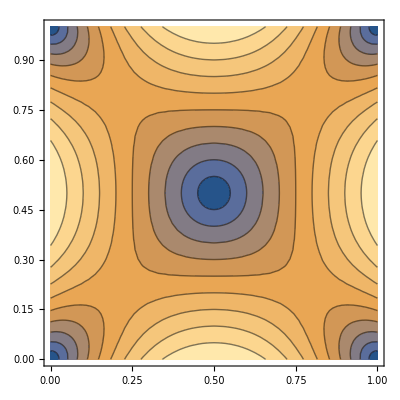

```mathematica
ContourPlot[Sqrt[(-perm (-1+2 x) (-1+y) y)^2+(-perm (-1+x) x (-1+2 y))^2]/.{ perm->1},{x,0,1},{y,0,1}]
```

### Source term f :

```mathematica
Sigma[x,y]
```

{{alpha x y (-1+x+y-x y)+2 (λ+μ),0},{0,alpha x y (-1+x+y-x y)+2 (λ+μ)}}

```mathematica
-(D[alpha x y (-1+x+y-x y)+2 (λ+μ),x]+D[0,y])//Simplify
```

alpha (-1+2 x) (-1+y) y

```mathematica
f1[y_]:=alpha (-1+2 x) (-1+y) y
```

```mathematica
-(D[0,x]+D[alpha x y (-1+x+y-x y)+2 (λ+μ),y])//Simplify
```

alpha (-1+x) x (-1+2 y)

```mathematica
f2[x_]:=alpha (-1+x) x (-1+2 y)
```

### Source term q :

```mathematica
u[x,y]
```

{x,y}

```mathematica
z[x,y]
```

{-perm (-1+2 x) (-1+y) y,-perm (-1+x) x (-1+2 y)}

```mathematica
D[c0 p[x,y]+alpha (D[x,x]+D[y,y]),t]+D[-perm (-1+2 x) (-1+y) y,x]+D[-perm (-1+x) x (-1+2 y),y]/.{c0->0}//Simplify
```

-2 perm (-x+x^2+(-1+y) y)